```mathematica
Q[a_,h_,t_]:=a*h*t;
CylinderVolume[r_,h_]:=π*r^2*h;
CylinderHeight[v_,r_]:=v/(π r^2);
```

```mathematica
Solve[v==CylinderVolume[r,h],h]
```

{{h→v/(π r^2)}}

```mathematica
a1={#1,CylinderHeight[#2,0.5]}&@@@RecurrenceTable[{
x[1]==0,
x[n]==x[n-1]+0.1,
y[1]==CylinderVolume[0.5, 2],
y[n]==y[n-1]-Q[1.0,CylinderHeight[y[n-1],0.5], 0.1]
}, {x,y},{n,1,10000}];
```

```mathematica
a2={#1,CylinderHeight[#2,0.5]}&@@@RecurrenceTable[{
x[1]==0,
x[n]==x[n-1]+0.1,
y[1]==CylinderVolume[0.5, 2],
y[n]==y[n-1]-Q[0.1,CylinderHeight[y[n-1],0.5], 0.1]
}, {x,y},{n,1,10000}];
a3={#1,CylinderHeight[#2,0.5]}&@@@RecurrenceTable[{
x[1]==0,
x[n]==x[n-1]+0.1,
y[1]==CylinderVolume[0.5, 2],
y[n]==y[n-1]-Q[0.01,CylinderHeight[y[n-1],0.5], 0.1]
}, {x,y},{n,1,10000}];
```

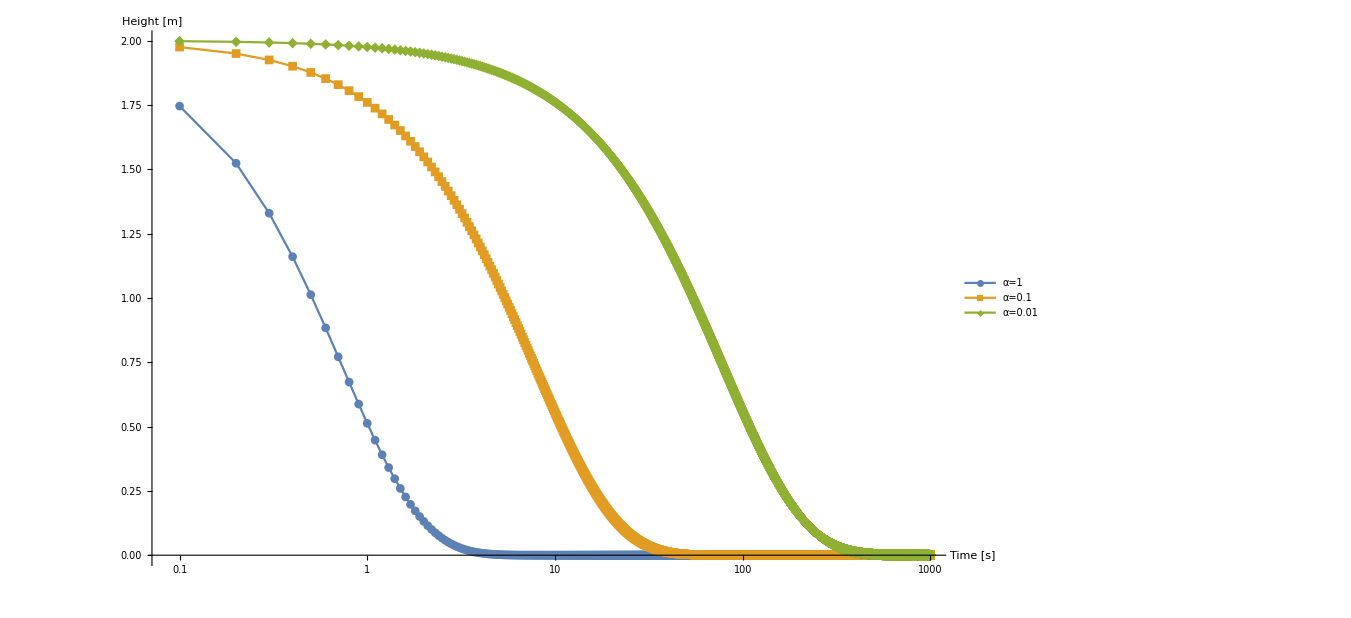

Cylinder.pdf

```mathematica
ListLogLinearPlot[{a1,a2,a3},PlotRange->Full,Joined->True,PlotMarkers->Automatic,AxesLabel->{"Time [s]","Height [m]"},LabelStyle->Large,PlotLegends->{"α=1","α=0.1","α=0.01"}, ImageSize->1000]
Export["Cylinder.pdf",%]
```

```mathematica
ConeVolume[r_,h_]:=1/3*π*r^2*h;
ConeHeight[v_,r_]:=(3 v)/(π r^2);
```

```mathematica
Solve[v==ConeVolume[r,h],h]
```

{{h→(3 v)/(π r^2)}}

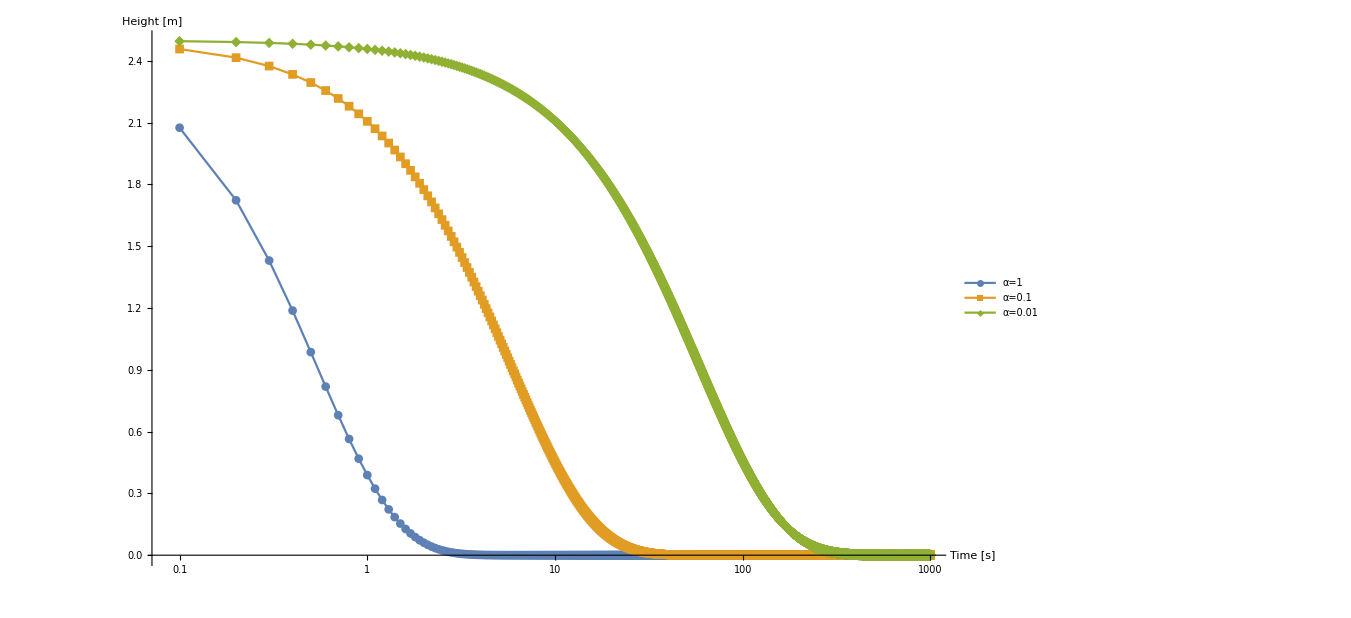

Cone.pdf

```mathematica
b1={#1,ConeHeight[#2,0.75]}&@@@RecurrenceTable[{
x[1]==0,
x[n]==x[n-1]+0.1,
y[1]==ConeVolume[0.75, 2.5],
y[n]==y[n-1]-Q[1.0,ConeHeight[y[n-1],0.75], 0.1]
}, {x,y},{n,1,10000}];
b2={#1,ConeHeight[#2,0.75]}&@@@RecurrenceTable[{
x[1]==0,
x[n]==x[n-1]+0.1,
y[1]==ConeVolume[0.75, 2.5],
y[n]==y[n-1]-Q[0.1,ConeHeight[y[n-1],0.75], 0.1]
}, {x,y},{n,1,10000}];
b3={#1,ConeHeight[#2,0.75]}&@@@RecurrenceTable[{
x[1]==0,
x[n]==x[n-1]+0.1,
y[1]==ConeVolume[0.75, 2.5],
y[n]==y[n-1]-Q[0.01,ConeHeight[y[n-1],0.75], 0.1]
}, {x,y},{n,1,10000}];
ListLogLinearPlot[{b1,b2,b3},PlotRange->Full,Joined->True,PlotMarkers->Automatic,AxesLabel->{"Time [s]","Height [m]"},LabelStyle->Large,PlotLegends->{"α=1","α=0.1","α=0.01"}, ImageSize->1000]
Export["Cone.pdf",%]
```

```mathematica
α=1.0;
τ=0.1;
c1=RecurrenceTable[{
x[1]==0,
x[n]==x[n-1]+0.1,
y1[1]==CylinderVolume[0.5, 2],
y1[n]==y1[n-1]-Q[α,CylinderHeight[y1[n-1],0.5], τ],
y2[1]==0,
y2[n]==Q[α,CylinderHeight[y1[n-1],0.5], τ]+y2[n-1]-Q[α,ConeHeight[y2[n-1],0.75], τ]
}, {x,y1,y2},{n,1,10000}];
c11={#1,CylinderHeight[#2,0.5]}&@@@c1;
c12={#1,ConeHeight[#3,0.75]}&@@@c1;

α=0.1;
c2=RecurrenceTable[{
x[1]==0,
x[n]==x[n-1]+0.1,
y1[1]==CylinderVolume[0.5, 2],
y1[n]==y1[n-1]-Q[α,CylinderHeight[y1[n-1],0.5], τ],
y2[1]==0,
y2[n]==Q[α,CylinderHeight[y1[n-1],0.5], τ]+y2[n-1]-Q[α,ConeHeight[y2[n-1],0.75], τ]
}, {x,y1,y2},{n,1,10000}];
c21={#1,CylinderHeight[#2,0.5]}&@@@c2;
c22={#1,ConeHeight[#3,0.75]}&@@@c2;

α=0.01;
c3=RecurrenceTable[{
x[1]==0,
x[n]==x[n-1]+0.1,
y1[1]==CylinderVolume[0.5, 2],
y1[n]==y1[n-1]-Q[α,CylinderHeight[y1[n-1],0.5], τ],
y2[1]==0,
y2[n]==Q[α,CylinderHeight[y1[n-1],0.5], τ]+y2[n-1]-Q[α,ConeHeight[y2[n-1],0.75], τ]
}, {x,y1,y2},{n,1,10000}];
c31={#1,CylinderHeight[#2,0.5]}&@@@c3;
c32={#1,ConeHeight[#3,0.75]}&@@@c3;
```

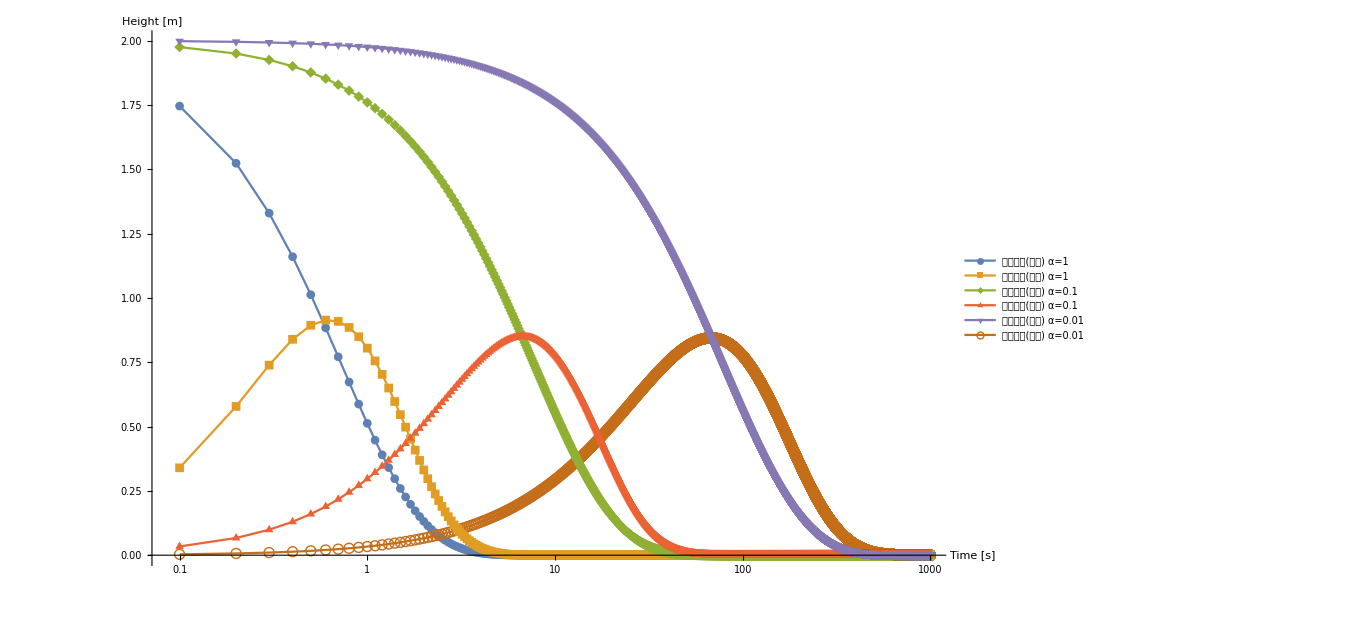

Merge.pdf

```mathematica
ListLogLinearPlot[{c11,c12,c21,c22,c31,c32},PlotRange->Full,Joined->True,PlotMarkers->Automatic,AxesLabel->{"Time [s]","Height [m]"},LabelStyle->Large,PlotLegends->{"水タンク(円柱) α=1","水タンク(円錐) α=1","水タンク(円柱) α=0.1","水タンク(円錐) α=0.1","水タンク(円柱) α=0.01","水タンク(円錐) α=0.01"}, ImageSize->1000]
Export["Merge.pdf",%]
```